## Prueba

```mathematica
(*1. Cargar el paquete (asegúrate de que el archivo.wl esté en el mismo directorio o en el Path)*)
<<QMB`
```

```mathematica
?QuantumGameOfLifeHamiltonian
```

```mathematica
(*2. Definir parámetros del sistema*)
L=3;
```

```mathematica
(*3. Generar el Hamiltoniano por sectores*)
AbsoluteTiming[H=QuantumGameOfLifeHamiltonian[L]]
```

{0.001091,SparseArray[…]}

```mathematica
H.{1,0,0,0,0,0,0,0}
H.{0,0,1,0,0,0,0,0}
```

{0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,1.,0.,0.,1.,0.}

```mathematica
Tuples[{0,1},L]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

## L=15, k=0, p=+1

```mathematica
(*1. Cargar el paquete (asegúrate de que el archivo.wl esté en el mismo directorio o en el Path)*)
<<QMB`
```

```mathematica
?QuantumGameOfLifeHamiltonian
```

```mathematica
(*2. Definir parámetros del sistema*)
L=15; 
k=0;  
p=1;
```

```mathematica
(*3. Generar el Hamiltoniano por sectores*)
(*Esta función usa la implementación bitwise optimizada que acabamos de crear*)
AbsoluteTiming[Hsector=QuantumGameOfLifeHamiltonian[L,Momentum->k,Parity->p]]
```

{28.3477,SparseArray[…]}

```mathematica
(*4. Diagonalización Exacta*)
evals=Sort[Eigenvalues[Normal@Hsector]];
```

```mathematica
(*5. Desdoblar el espectro*)
unfolded=Unfold[evals];
```

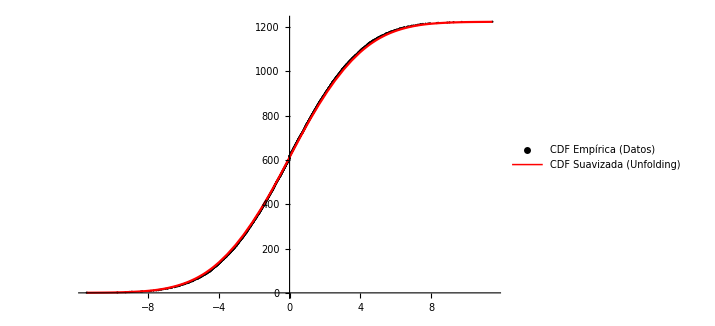

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[Unfold[evals]["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

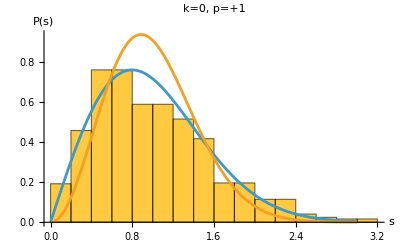

```mathematica
Show[
Histogram[Differences[unfolded["UnfoldedLevels"]],Automatic,"PDF",PlotLabel->"k=0, p=+1",AxesLabel->{"s", "P(s)"},LabelStyle->Directive[Black,16]],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π]},{s,0,3}]
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

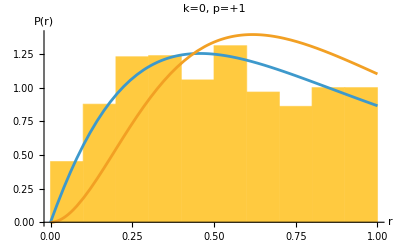

```mathematica
(*6. Visualización (Opcional)*)
(*Histograma de los espaciamientos normalizados*)
ratios=NormalizedSpacingRatios[evals,1]; 
Show[Histogram[ratios,Automatic,"PDF",PlotLabel->"k=0, p=+1",AxesLabel->{"r", "P(r)"},LabelStyle->Directive[Black,16]],
Plot[{2*RatiosDistribution[r,1],2*RatiosDistribution[r,2.]},{r,0,1}]
]
```

## L=15, k=1

```mathematica
(*1. Cargar el paquete (asegúrate de que el archivo.wl esté en el mismo directorio o en el Path)*)
<<QMB`
```

```mathematica
?QuantumGameOfLifeHamiltonian
```

```mathematica
(*2. Definir parámetros del sistema*)
L=15; 
k=1;
```

```mathematica
(*3. Generar el Hamiltoniano por sectores*)
(*Esta función usa la implementación bitwise optimizada que acabamos de crear*)
AbsoluteTiming[Hsector=QuantumGameOfLifeHamiltonian[L,Momentum->k]]
```

{4.02363,SparseArray[<20322>, {2182, 2182}]}

```mathematica
(*4. Diagonalización Exacta*)
evals=Sort[Eigenvalues[Normal@Hsector]];
```

```mathematica
(*5. Desdoblar el espectro*)
unfolded=Unfold[evals];
```

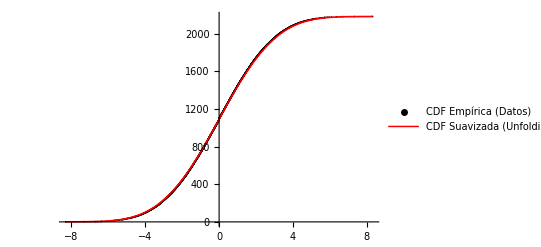

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[Unfold[evals]["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

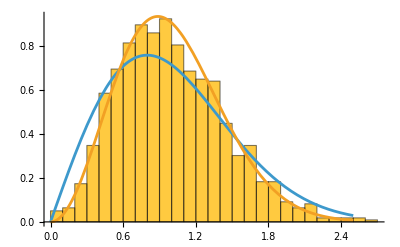

```mathematica
Show[
Histogram[Differences[unfolded["UnfoldedLevels"]],Automatic,"PDF",PlotLabel->"",AxesLabel->{"", ""},LabelStyle->Directive[Black,16]],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π]},{s,0,2.5}]
]
```

## L=15, k=2

```mathematica
(*1. Cargar el paquete (asegúrate de que el archivo.wl esté en el mismo directorio o en el Path)*)
<<QMB`
```

```mathematica
(*2. Definir parámetros del sistema*)
L=15; 
k=2;
```

```mathematica
(*3. Generar el Hamiltoniano por sectores*)
(*Esta función usa la implementación bitwise optimizada que acabamos de crear*)
AbsoluteTiming[Hsector=QuantumGameOfLifeHamiltonian[L,Momentum->k]]
```

{3.86597,SparseArray[<20322>, {2182, 2182}]}

```mathematica
(*4. Diagonalización Exacta*)
evals=Chop@Sort[Eigenvalues[Normal@Hsector]];
```

```mathematica
(*5. Desdoblar el espectro*)
unfolded=Unfold[evals];
```

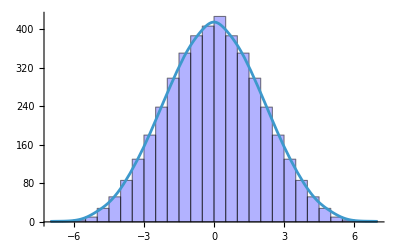

```mathematica
Show[
Histogram[evals,Automatic,"Intensity",ChartStyle->Directive[Opacity[0.3],Blue],LabelStyle->{FontFamily->"Latin Modern Math",14}],
Plot[unfolded["SmoothPDF"][x],{x,-7,7}]
]
```

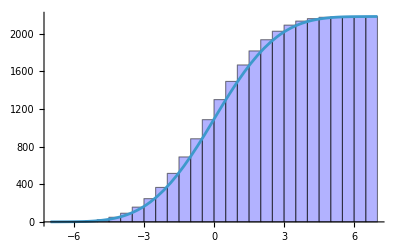

```mathematica
Show[
Histogram[evals,Automatic,"CumulativeCount",ChartStyle->Directive[Opacity[0.3],Blue],LabelStyle->{FontFamily->"Latin Modern Math",14}],
Plot[unfolded["SmoothCDF"][x],{x,-7,7}]
]
```

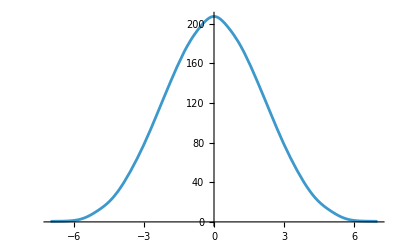

```mathematica
Plot[unfolded["SmoothPDF"][x]/2,{x,-7,7}]
```

```mathematica
NIntegrate[unfolded["SmoothPDF"][x],{x,-10,10}]
```

2182.

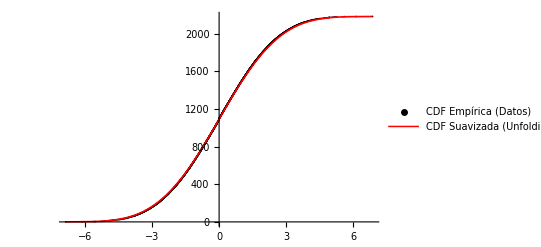

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[Unfold[evals]["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

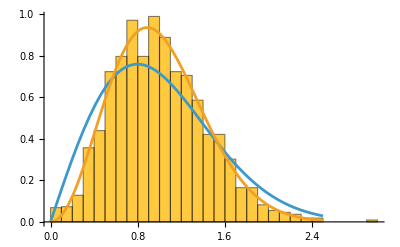

```mathematica
Show[
Histogram[Differences[unfolded["UnfoldedLevels"]],Automatic,"PDF",PlotLabel->"",AxesLabel->{"", ""},LabelStyle->Directive[Black,16]],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π]},{s,0,2.5}]
]
```

## L=15, k=5

```mathematica
(*1. Cargar el paquete (asegúrate de que el archivo.wl esté en el mismo directorio o en el Path)*)
<<QMB`
```

```mathematica
?QuantumGameOfLifeHamiltonian
```

```mathematica
(*2. Definir parámetros del sistema*)
L=15; 
k=8;
```

```mathematica
(*3. Generar el Hamiltoniano por sectores*)
(*Esta función usa la implementación bitwise optimizada que acabamos de crear*)
AbsoluteTiming[Hsector=QuantumGameOfLifeHamiltonian[L,Momentum->k]]
```

{3.88833,SparseArray[<20322>, {2182, 2182}]}

```mathematica
(*4. Diagonalización Exacta*)
evals=Chop@Sort[Eigenvalues[Normal@Hsector]];
```

```mathematica
(*5. Desdoblar el espectro*)
unfolded=Unfold[evals];
```

```mathematica
(* Comparar la función de conteo N(E) para ver si el unfolding fue bueno*)
n=Length[evals];
Show[
ListPlot[Transpose[{evals,Range[n]}],PlotStyle->{Black,PointSize[0.003]},Joined->False,(*Puntos discretos para ver la escalera*)PlotLegends->{"CDF Empírica (Datos)"}],
Plot[Unfold[evals]["SmoothCDF"][e],{e,Min[evals],Max[evals]},PlotStyle->{Red,Thickness[0.003]},PlotLegends->{"CDF Suavizada (Unfolding)"}]
]
```

-Graphics-

```mathematica
Show[
Histogram[Differences[unfolded["UnfoldedLevels"]],Automatic,"PDF",PlotLabel->"",AxesLabel->{"", ""},LabelStyle->Directive[Black,16]],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],(32/π^2) s^2 Exp[-(4 s^2)/π]},{s,0,2.5}]
]
```

-Graphics-